```mathematica
Binarize
```

```mathematica
Binarize[ImageResize[CurrentImage[],{15,15}],1]
```

-Graphics-

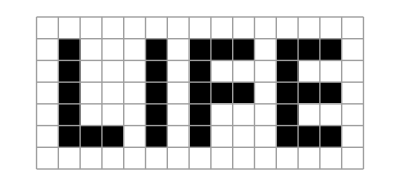
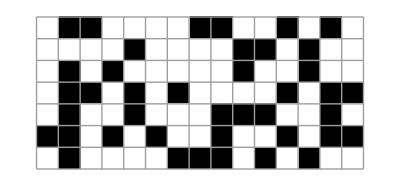
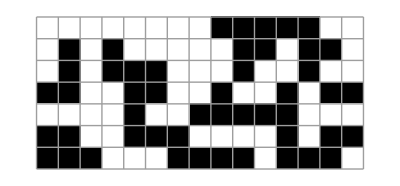
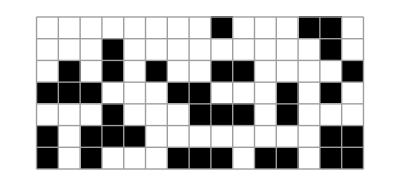
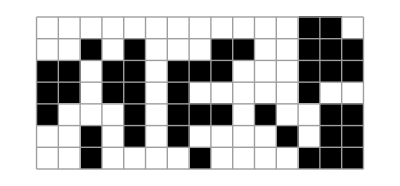
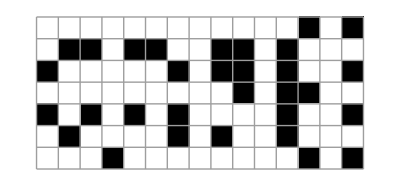
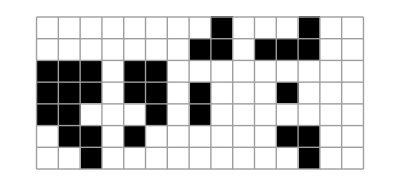
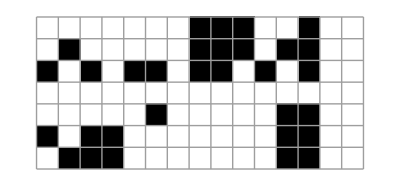
{98.0816,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
lr;Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf6.m"];
LIFE=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 1, 1, 0, 1, 1, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 1, 1, 0, 1, 1, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0}, {0, 1, 1, 1, 0, 1, 0, 1, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
(*LIFE=({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 1, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0}, {0, 1, 0, 0, 0, 1, 0}, {0, 0, 1, 1, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}});*)
(*xPArray=RandomInteger[{0,1},{6,6}];
*)(*updateIJ[xPAay]*)
AbsoluteTiming[{LIFE//plt,lifePlot[XX0=updateIJ[LIFE],9]}]
```

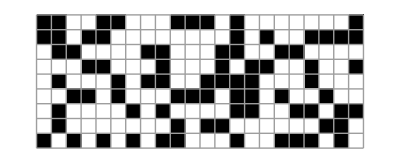
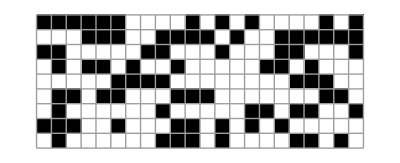
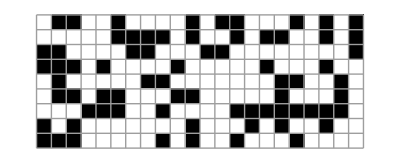
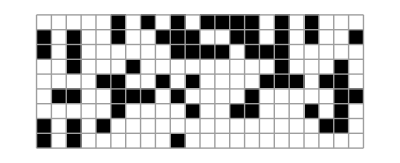
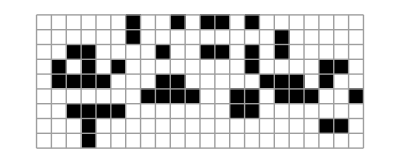
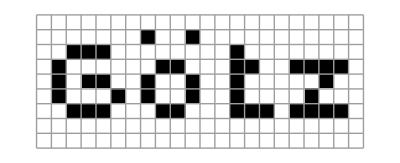
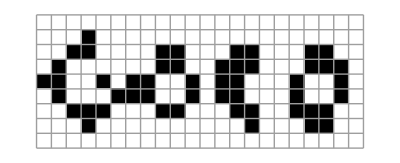
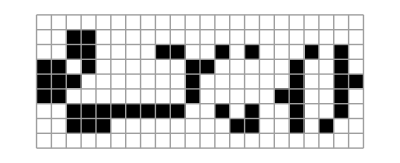

```mathematica
FRAMES=lifePlot[XX0,42]
```

```mathematica
X0=updateIJ[LIFE];
```

Set::wrsym: Symbol False is Protected.

General::stop: Further output of Set::wrsym will be suppressed during this calculation.

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf6.m"];
updateIJ[({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}})]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
Clear[i,j,x2];
count[{2,3},{{i,j}[[1]],{i,js}[[2]]},x2]
```

```mathematica
lr
```

and::shdw: Symbol and appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

```mathematica
Get[]
```

```mathematica
Clear[x0,x1,x2,x3,x4]CopyToClipboard[BooleanConvert[(and@{Nothing,          ,(x3[i,j]&&count[{2,3},{i,j},x3])~Implies~xp[i,j]
        ,(x3[i,j]&&!count[{2,3},{i,j},x3])~Implies~!xp[i,j]
        ,(!x3[i,j]&&count[{3},{i,j},x3])~Implies~xp[i,j]
        ,(!x3[i,j]&&!count[{3},{i,j},x3])~Implies~!xp[i,j]
}),
"CNF"]];
```